```mathematica
EntityProperties["AdministrativeDivision"]
```

{accommodation and food services sales,number of aggravated assaults,rate of aggravated assault,aggregate household income,annual births,annual deaths,housing units change rate,area,average ACT composite score,average ACT English score,average ACT math score,average ACT reading score,average ACT science score,average commute time,average home sale price,average SAT reading score,average SAT math score,average SAT writing score,average total SAT score,bordering counties,bordering states,number of burglaries,rate of burglary,number of businesses,business ownership by ethnicity,Amerindian business ownership fraction,Asian business ownership fraction,black business ownership fraction,Hispanic business ownership fraction,Pacific Islander business ownership fraction,white business ownership fraction,business ownership by gender,capital city,capital name,civilian labor force,civilian unemployment rate,coincident economic activity index,coordinates,country,county sales tax rate,total rate of crime,total number of crimes,disabled people,district court,earnings,average earnings per job,employment,employment change,farmland area,federal government expenditure,federal government expenditure per capita,FIPS code,flag,number of rapes,rate of rape,fraction foreign born,high school graduates taking ACT,high school graduates taking SAT,Gini index,government employment,GDP,GSP,has polygon?,insured population fraction,people with health insurance,people without health insurance,uninsured population fraction,highest elevation,highest point,highest sales tax rate,home ownership rate,home vacancy rate,house price index,housing permits,housing starts,households,housing units change,housing in multiple unit structures,infant deaths,land area,number of larcenies,rate of larceny,latitude,longitude,lowest elevation,lowest point,lowest sales tax rate,manufacturing value of shipments,mean elevation,median age,median household income,median home sale price,median total sales tax rate,minimum wage,number of motor vehicle thefts,rate of motor vehicle thefts,state mottoes,incidents of murder and nonnegligent manslaughter,rate of murder and nonnegligent manslaughter,name,new housing units,new housing units value,state nicknames,nonemployer businesses,median owner-occupied home value,owner-occupied housing,parent region,per capita income,per capita personal income,people per household,polygon,population,population by educational attainment,population by migration in previous 12 months,population by language spoken at home,population by marital status,population by poverty status,population by school enrollment,population density,position,private non-farm employment,private non-farm employment change,private non-farm businesses,total rate of property crime,total number of property crimes,residential rental vacancy rate,4 bedroom apartment fair market rent,1 bedroom apartment fair market rent,3 bedroom apartment fair market rent,2 bedroom apartment fair market rent,studio apartment fair market rent,retail sales,retail sales per capita,number of robberies,rate of robbery,state slogan,state song,abbreviation,state government tax collections,state sales tax rate,subdivisions,time zones,total voter registration rate,total voting rate,state tree,unweighted sample housing units,unweighted sample population,total rate of violent crime,total number of violent crimes,wholesale sales,employment,ZIP codes}

```mathematica
%70[[5]]//Head
```

EntityProperty

```mathematica
usstates=EntityList[EntityClass["AdministrativeDivision","ContinentalUSStates"]];
```

```mathematica
EntityValue[category[[1]],"Definition"]
```

```mathematica
category2=Select[EntityProperties["AdministrativeDivision"],StringContainsQ[CanonicalName[#], "Educational"]&][[1]]
```

```mathematica
GeoRegionValuePlot[usstates->category2,ColorFunctionScaling->True]
```

```mathematica
(* 
annual births-deaths-population - health insurance - "civilian unemployment rate", employment - "uninsured population fraction" "people with/out health insurance "home ownership rate""   "home vacancy rate"
"infant deaths" "minimum wage" "per capita income" "population by poverty status" "population density" "position"
*)
```

```mathematica
(* annual deaths / population = % of people per state who die every year *)
```

```mathematica
(* people without health insurance / population = % of people who do not have health insurance *)
```

```mathematica
(* other stuff that may be interesting from the above list *)
```

```mathematica
(* Preliminary for CE: *)
```

```mathematica
populationentity = Select[EntityProperties["AdministrativeDivision"],StringContainsQ[CanonicalName[#], "Population"]&][[1]]
```

population

```mathematica
populationvalue =EntityValue[usstates,populationentity];
```

```mathematica
deathsentity=  Select[EntityProperties["AdministrativeDivision"],StringContainsQ[CanonicalName[#], "Deaths"]&][[1]]
```

annual deaths

```mathematica
deathsvalue = EntityValue[usstates,deathsentity]/populationvalue//Normalize;
```

```mathematica
nohientity = Select[EntityProperties["AdministrativeDivision"],StringContainsQ[CanonicalName[#], "Insurance"]&][[3]]
```

people without health insurance

```mathematica
nohivalue = EntityValue[usstates,nohientity]/populationvalue//Normalize;
```

```mathematica
data = Table[{usstates[[i]],nohivalue[[i]],deathsvalue[[i]]},{i,Length[usstates]}];
```

```mathematica
data[[All,3]]//N//Sort//Reverse
```

{0.194042,0.173927,0.166295,0.166016,0.165507,0.164961,0.16463,0.16363,0.162804,0.161116,0.159599,0.158064,0.155979,0.15495,0.154496,0.152015,0.151889,0.148754,0.147588,0.146685,0.144482,0.144061,0.141243,0.140254,0.137888,0.137875,0.137646,0.137602,0.137437,0.136431,0.135599,0.135342,0.134496,0.133739,0.133583,0.133393,0.130822,0.130787,0.130185,0.129444,0.129134,0.128713,0.123089,0.122744,0.116231,0.113674,0.112502,0.090674}

```mathematica
badfit = Fit[data[[All,2;;]],{1,x},x]
```

0.142079+0.00783509 x

```mathematica
plt1=ListPlot[data[[All,2;;3]],PlotRange->All];
```

```mathematica
plt2 = Plot[badfit,{x,Min[data[[All,2]]],Max[data[[All,2]]]}];
```

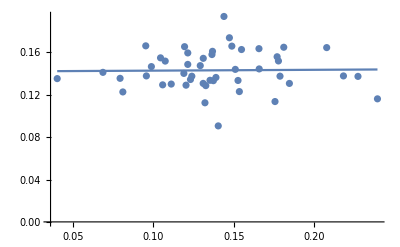

```mathematica
Show[plt1,plt2]
```

```mathematica
Correlation[deathsvalue,nohivalue]
```

0.0168384

```mathematica
GeoRegionValuePlot[...]
```

```mathematica
(* Choose some other quantities, create correlation plots *)
```

```mathematica
(* Test ALL the features. Show the ones with the largest correlation *)
```

```mathematica
(* Will have to normalise some to population etc etc *)
```

```mathematica
(* New Round *)
```

```mathematica
(*allentities = EntityProperties["AdministrativeDivision"][[;;6]] *)
```

```mathematica
allentities=Select[EntityProperties["AdministrativeDivision"],StringContainsQ[CanonicalName[#], "Rate"]&]
```

{rate of aggravated assault,rate of burglary,civilian unemployment rate,county sales tax rate,total rate of crime,rate of rape,insured population fraction,uninsured population fraction,highest sales tax rate,home ownership rate,home vacancy rate,rate of larceny,lowest sales tax rate,median total sales tax rate,rate of motor vehicle thefts,rate of murder and nonnegligent manslaughter,total rate of property crime,residential rental vacancy rate,rate of robbery,state sales tax rate,total voter registration rate,total voting rate,total rate of violent crime}

```mathematica
allentities=Delete[allentities,4];
```

```mathematica
Length[allentities]
```

22

```mathematica
usstates=EntityList[EntityClass["AdministrativeDivision","ContinentalUSStates"]];
```

```mathematica
alldata=Table[{usstates[[i]],allentities[[j]]},{i,Length[usstates]},{j,Length[allentities]}];
```

```mathematica
alldata//Dimensions
```

{48,22,2}

```mathematica
(* Normalise by population here, if needed *)
```

```mathematica
allvalues= Apply[EntityValue,alldata,{2}]//QuantityMagnitude;
```

```mathematica
(* entityvalue [v, "GDB"] *)
```

```mathematica
allvalues//Dimensions
```

{48,22}

```mathematica
correlations=Table[{allentities[[i]],allentities[[j]],Correlation[allvalues[[All,i]],allvalues[[All,j]]]},{i,Length[allentities]},{j,i-1}];
```

```mathematica
correlations//N// Flatten//TraditionalForm
```

```mathematica
Flatten[correlations,1]//SortBy[Abs[#[[3]]]&]//Reverse//Column
```

{uninsured population fraction,insured population fraction,-1.}
{total rate of property crime,total rate of crime,0.990104}
{total rate of violent crime,rate of aggravated assault,0.96932}
{total rate of property crime,rate of larceny,0.968361}
{rate of larceny,total rate of crime,0.950705}
{median total sales tax rate,highest sales tax rate,0.932533}
{total voting rate,total voter registration rate,0.926396}
{state sales tax rate,lowest sales tax rate,0.900283}
{total rate of crime,rate of burglary,0.858729}
{total rate of property crime,rate of burglary,0.854384}
{median total sales tax rate,lowest sales tax rate,0.814546}
{rate of motor vehicle thefts,total rate of crime,0.800357}
{total rate of property crime,rate of motor vehicle thefts,0.79985}
{total rate of violent crime,total rate of crime,0.783738}
{total rate of crime,rate of aggravated assault,0.756099}
{state sales tax rate,median total sales tax rate,0.754727}
{residential rental vacancy rate,home vacancy rate,0.731359}
{rate of larceny,rate of burglary,0.730258}
{total rate of violent crime,rate of murder and nonnegligent manslaughter,0.727023}
{rate of motor vehicle thefts,rate of larceny,0.706997}
{total rate of violent crime,rate of robbery,0.700086}
{rate of murder and nonnegligent manslaughter,rate of burglary,0.690882}
{total rate of violent crime,total rate of property crime,0.688823}
{lowest sales tax rate,highest sales tax rate,0.680355}
{total rate of property crime,rate of aggravated assault,0.663494}
{rate of robbery,rate of murder and nonnegligent manslaughter,0.660923}
{rate of murder and nonnegligent manslaughter,rate of aggravated assault,0.658655}
{total rate of violent crime,rate of burglary,0.654638}
{rate of murder and nonnegligent manslaughter,total rate of crime,0.64941}
{rate of burglary,rate of aggravated assault,0.63749}
{total rate of violent crime,rate of larceny,0.625327}
{state sales tax rate,highest sales tax rate,0.614211}
{rate of larceny,rate of aggravated assault,0.613462}
{uninsured population fraction,total rate of crime,0.609344}
{insured population fraction,total rate of crime,-0.609344}
{rate of motor vehicle thefts,rate of burglary,0.604157}
{total rate of property crime,uninsured population fraction,0.597723}
{total rate of property crime,insured population fraction,-0.597723}
{total rate of violent crime,rate of motor vehicle thefts,0.594462}
{total rate of property crime,rate of murder and nonnegligent manslaughter,0.593714}
{uninsured population fraction,rate of burglary,0.581309}
{insured population fraction,rate of burglary,-0.581309}
{rate of motor vehicle thefts,uninsured population fraction,0.54521}
{rate of motor vehicle thefts,insured population fraction,-0.54521}
{total voter registration rate,home ownership rate,0.536603}
{rate of murder and nonnegligent manslaughter,rate of larceny,0.533833}
{total voting rate,uninsured population fraction,-0.532529}
{total voting rate,insured population fraction,0.532529}
{rate of larceny,uninsured population fraction,0.528381}
{rate of larceny,insured population fraction,-0.528381}
{rate of robbery,total rate of crime,0.523729}
{rate of motor vehicle thefts,rate of aggravated assault,0.522795}
{rate of robbery,rate of aggravated assault,0.515879}
{rate of robbery,civilian unemployment rate,0.510734}
{total voter registration rate,uninsured population fraction,-0.508386}
{total voter registration rate,insured population fraction,0.508386}
{total rate of violent crime,insured population fraction,-0.502314}
{total rate of violent crime,uninsured population fraction,0.502314}
{total rate of violent crime,total voting rate,-0.501014}
{residential rental vacancy rate,rate of aggravated assault,0.498768}
{residential rental vacancy rate,rate of burglary,0.493805}
{residential rental vacancy rate,rate of murder and nonnegligent manslaughter,0.488399}
{total voting rate,rate of robbery,-0.487567}
{total voter registration rate,rate of robbery,-0.486598}
{rate of robbery,rate of motor vehicle thefts,0.482542}
{rate of murder and nonnegligent manslaughter,civilian unemployment rate,0.4812}
{civilian unemployment rate,rate of burglary,0.475799}
{insured population fraction,rate of aggravated assault,-0.456972}
{uninsured population fraction,rate of aggravated assault,0.456972}
{total voting rate,rate of aggravated assault,-0.456697}
{rate of robbery,total rate of property crime,0.453108}
{rate of motor vehicle thefts,rate of rape,0.452361}
{residential rental vacancy rate,total rate of crime,0.452296}
{median total sales tax rate,rate of burglary,0.452031}
{rate of murder and nonnegligent manslaughter,uninsured population fraction,0.446956}
{rate of murder and nonnegligent manslaughter,insured population fraction,-0.446956}
{total rate of crime,civilian unemployment rate,0.441737}
{highest sales tax rate,rate of burglary,0.441263}
{total rate of violent crime,residential rental vacancy rate,0.440017}
{total rate of property crime,civilian unemployment rate,0.42946}
{rate of murder and nonnegligent manslaughter,median total sales tax rate,0.429185}
{residential rental vacancy rate,total rate of property crime,0.428494}
{rate of robbery,rate of burglary,0.428392}
{uninsured population fraction,civilian unemployment rate,0.419637}
{insured population fraction,civilian unemployment rate,-0.419637}
{residential rental vacancy rate,rate of larceny,0.406706}
{total voting rate,median total sales tax rate,-0.406104}
{home vacancy rate,rate of aggravated assault,0.398396}
{rate of rape,rate of aggravated assault,0.397291}
{highest sales tax rate,total rate of crime,0.396022}
{rate of murder and nonnegligent manslaughter,highest sales tax rate,0.393561}
{total voting rate,home ownership rate,0.393109}
{total rate of violent crime,highest sales tax rate,0.388932}
{total rate of violent crime,total voter registration rate,-0.388464}
{rate of robbery,rate of larceny,0.386241}
{rate of robbery,uninsured population fraction,0.384388}
{rate of robbery,insured population fraction,-0.384388}
{total rate of violent crime,civilian unemployment rate,0.381196}
{rate of motor vehicle thefts,civilian unemployment rate,0.376024}
{total rate of violent crime,median total sales tax rate,0.37569}
{rate of rape,total rate of crime,0.37554}
{total rate of property crime,highest sales tax rate,0.374355}
{highest sales tax rate,rate of aggravated assault,0.372678}
{rate of robbery,home ownership rate,-0.369289}
{total voter registration rate,rate of motor vehicle thefts,-0.361811}
{total rate of violent crime,rate of rape,0.358485}
{rate of larceny,civilian unemployment rate,0.358341}
{total rate of property crime,rate of rape,0.357327}
{total voting rate,rate of motor vehicle thefts,-0.354239}
{home vacancy rate,uninsured population fraction,0.352448}
{home vacancy rate,insured population fraction,-0.352448}
{median total sales tax rate,total rate of crime,0.350971}
{total voting rate,civilian unemployment rate,-0.347887}
{total voting rate,highest sales tax rate,-0.34649}
{median total sales tax rate,rate of aggravated assault,0.342722}
{rate of robbery,median total sales tax rate,0.33669}
{total voting rate,total rate of crime,-0.333712}
{rate of murder and nonnegligent manslaughter,rate of motor vehicle thefts,0.333452}
{home vacancy rate,rate of burglary,0.328928}
{total rate of property crime,median total sales tax rate,0.324763}
{residential rental vacancy rate,highest sales tax rate,0.324095}
{total voter registration rate,rate of aggravated assault,-0.320824}
{total rate of violent crime,home vacancy rate,0.319917}
{total voter registration rate,median total sales tax rate,-0.316775}
{rate of larceny,rate of rape,0.316606}
{total voting rate,home vacancy rate,-0.314234}
{total voting rate,lowest sales tax rate,-0.31304}
{rate of murder and nonnegligent manslaughter,home vacancy rate,0.312383}
{rate of larceny,highest sales tax rate,0.310781}
{insured population fraction,rate of rape,-0.3012}
{uninsured population fraction,rate of rape,0.3012}
{home vacancy rate,highest sales tax rate,0.295037}
{rate of motor vehicle thefts,highest sales tax rate,0.292172}
{residential rental vacancy rate,median total sales tax rate,0.288577}
{civilian unemployment rate,rate of aggravated assault,0.28738}
{total voting rate,rate of burglary,-0.286908}
{home vacancy rate,total rate of crime,0.282413}
{total voter registration rate,civilian unemployment rate,-0.278783}
{residential rental vacancy rate,uninsured population fraction,0.277555}
{residential rental vacancy rate,insured population fraction,-0.277555}
{total voting rate,total rate of property crime,-0.276302}
{total voter registration rate,highest sales tax rate,-0.274228}
{rate of robbery,highest sales tax rate,0.269006}
{total voting rate,state sales tax rate,-0.265005}
{rate of rape,rate of burglary,0.264623}
{total voting rate,rate of murder and nonnegligent manslaughter,-0.264279}
{total rate of property crime,home vacancy rate,0.257344}
{median total sales tax rate,rate of larceny,0.244447}
{highest sales tax rate,uninsured population fraction,0.243987}
{highest sales tax rate,insured population fraction,-0.243987}
{rate of robbery,lowest sales tax rate,0.241827}
{median total sales tax rate,civilian unemployment rate,0.241374}
{total voter registration rate,total rate of crime,-0.236332}
{total voter registration rate,lowest sales tax rate,-0.235113}
{rate of motor vehicle thefts,median total sales tax rate,0.234113}
{rate of motor vehicle thefts,home ownership rate,-0.233735}
{rate of larceny,home vacancy rate,0.233444}
{residential rental vacancy rate,home ownership rate,0.223572}
{median total sales tax rate,home ownership rate,-0.223347}
{median total sales tax rate,insured population fraction,-0.220012}
{median total sales tax rate,uninsured population fraction,0.220012}
{median total sales tax rate,home vacancy rate,0.219598}
{lowest sales tax rate,rate of burglary,0.21947}
{total voter registration rate,home vacancy rate,-0.211971}
{lowest sales tax rate,civilian unemployment rate,0.20832}
{home vacancy rate,civilian unemployment rate,0.207143}
{total voting rate,rate of larceny,-0.207045}
{home ownership rate,uninsured population fraction,-0.204708}
{home ownership rate,insured population fraction,0.204708}
{rate of murder and nonnegligent manslaughter,lowest sales tax rate,0.202664}
{highest sales tax rate,civilian unemployment rate,0.201061}
{total voter registration rate,total rate of property crime,-0.188072}
{home ownership rate,highest sales tax rate,-0.186733}
{total voter registration rate,state sales tax rate,-0.183264}
{lowest sales tax rate,home ownership rate,-0.183172}
{residential rental vacancy rate,rate of rape,0.18248}
{state sales tax rate,rate of robbery,0.181327}
{state sales tax rate,civilian unemployment rate,0.180514}
{residential rental vacancy rate,rate of motor vehicle thefts,0.172982}
{state sales tax rate,rate of burglary,0.169762}
{state sales tax rate,rate of murder and nonnegligent manslaughter,0.165856}
{highest sales tax rate,rate of rape,0.163027}
{state sales tax rate,rate of larceny,-0.161486}
{home ownership rate,civilian unemployment rate,-0.146542}
{total voter registration rate,rate of larceny,-0.135055}
{lowest sales tax rate,rate of rape,-0.134517}
{total rate of violent crime,lowest sales tax rate,0.131485}
{total voter registration rate,rate of burglary,-0.130955}
{total voting rate,residential rental vacancy rate,-0.130734}
{state sales tax rate,rate of rape,-0.128985}
{total rate of violent crime,home ownership rate,-0.127629}
{rate of robbery,rate of rape,-0.124309}
{rate of robbery,residential rental vacancy rate,0.10991}
{total voter registration rate,rate of murder and nonnegligent manslaughter,-0.109887}
{residential rental vacancy rate,lowest sales tax rate,0.108461}
{home ownership rate,rate of rape,0.106164}
{state sales tax rate,residential rental vacancy rate,0.100957}
{rate of motor vehicle thefts,home vacancy rate,0.0915477}
{lowest sales tax rate,rate of aggravated assault,0.0868226}
{total voter registration rate,rate of rape,0.0741866}
{total voter registration rate,residential rental vacancy rate,0.0651495}
{state sales tax rate,home ownership rate,-0.0610107}
{state sales tax rate,total rate of property crime,-0.0607211}
{home ownership rate,rate of burglary,0.0606502}
{total rate of violent crime,state sales tax rate,0.0593499}
{residential rental vacancy rate,civilian unemployment rate,0.054654}
{lowest sales tax rate,total rate of crime,0.0529071}
{lowest sales tax rate,rate of larceny,-0.0495398}
{home ownership rate,total rate of crime,-0.0494386}
{state sales tax rate,home vacancy rate,0.0477463}
{rate of murder and nonnegligent manslaughter,home ownership rate,0.0467666}
{lowest sales tax rate,home vacancy rate,0.0448622}
{rate of murder and nonnegligent manslaughter,rate of rape,0.0407278}
{state sales tax rate,total rate of crime,-0.0405344}
{median total sales tax rate,rate of rape,0.0360457}
{rate of rape,civilian unemployment rate,-0.0343221}
{home ownership rate,rate of aggravated assault,-0.0333798}
{state sales tax rate,rate of motor vehicle thefts,-0.0328381}
{state sales tax rate,insured population fraction,0.0327923}
{state sales tax rate,uninsured population fraction,-0.0327923}
{total rate of property crime,lowest sales tax rate,0.032044}
{total rate of property crime,home ownership rate,-0.0288668}
{rate of robbery,home vacancy rate,0.0283299}
{home vacancy rate,home ownership rate,0.0253342}
{home vacancy rate,rate of rape,0.0183216}
{state sales tax rate,rate of aggravated assault,0.0166576}
{total voting rate,rate of rape,0.0118272}
{rate of motor vehicle thefts,lowest sales tax rate,0.00967433}
{rate of larceny,home ownership rate,-0.00571002}
{lowest sales tax rate,uninsured population fraction,0.00506732}
{lowest sales tax rate,insured population fraction,-0.00506732}